# Introduction to Wolfram Language

## Functions

All function use square brackets, and have names that starts with capital letters.

```mathematica
Times[2,Plus[3,4]]
```

14

```mathematica
Times[5,4,3,2]
```

120

```mathematica
Times[Plus[8,7], Plus[9,2]]
```

165

```mathematica
Apply[Times,Apply[Plus, {{8,7},{9,2}},2]]
```

165

```mathematica
Times@@Plus@@@{{8,7},{9,2}}
```

165

## Lists

```mathematica
ListPlot[Join[Range[20],Reverse[Range[20]],RandomInteger[20,20]],Filling->10,PlotTheme -> {"OpenMarkersThick", "LargeLabels"},FillingStyle->{Blue,Red},GridLines->{None,{{10,{Black,Thick}}}}]
```

-Graphics-

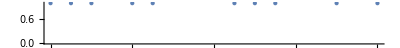

```mathematica
NumberLinePlot[RandomSample[Range[20],10]]
```

```mathematica
PieChart[Range[10],SectorOrigin->{Automatic,1},PerformanceGoal->"Quality"]
```

-Graphics-

```mathematica
Take[Range[10],5]
```

{1,2,3,4,5}

```mathematica
Drop[Range[10],5]
```

{6,7,8,9,10}

```mathematica
Rest[Range[10]]
```

{2,3,4,5,6,7,8,9,10}

```mathematica
Most[Range[10]]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
(* use table to make list*)
Table[{1,2},5]
```

{{1,2},{1,2},{1,2},{1,2},{1,2}}

```mathematica
Table[n-1,{n,1,10}]
```

{0,1,2,3,4,5,6,7,8,9}

```mathematica
Table[Range[n],{n,1,10}] //MatrixForm
```

({1}
{1,2}
{1,2,3}
{1,2,3,4}
{1,2,3,4,5}
{1,2,3,4,5,6}
{1,2,3,4,5,6,7}
{1,2,3,4,5,6,7,8}
{1,2,3,4,5,6,7,8,9}
{1,2,3,4,5,6,7,8,9,10})

```mathematica
Table[Range[n],{n,1,10}] // Column
```

{1}
{1,2}
{1,2,3}
{1,2,3,4}
{1,2,3,4,5}
{1,2,3,4,5,6}
{1,2,3,4,5,6,7}
{1,2,3,4,5,6,7,8}
{1,2,3,4,5,6,7,8,9}
{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[Column[Range[n]],{n,1,10}]
```

{1,1
2,1
2
3,1
2
3
4,1
2
3
4
5,1
2
3
4
5
6,1
2
3
4
5
6
7,1
2
3
4
5
6
7
8,1
2
3
4
5
6
7
8
9,1
2
3
4
5
6
7
8
9
10}

## Colors and Graphics

```mathematica
Table[RGBColor[0.5,g,0.5],{g,0,1,0.05}]
```

{RGBColor[0.5, 0., 0.5],RGBColor[0.5, 0.05, 0.5],RGBColor[0.5, 0.1, 0.5],RGBColor[0.5, 0.15000000000000002, 0.5],RGBColor[0.5, 0.2, 0.5],RGBColor[0.5, 0.25, 0.5],RGBColor[0.5, 0.30000000000000004, 0.5],RGBColor[0.5, 0.35000000000000003, 0.5],RGBColor[0.5, 0.4, 0.5],RGBColor[0.5, 0.45, 0.5],RGBColor[0.5, 0.5, 0.5],RGBColor[0.5, 0.55, 0.5],RGBColor[0.5, 0.6000000000000001, 0.5],RGBColor[0.5, 0.65, 0.5],RGBColor[0.5, 0.7000000000000001, 0.5],RGBColor[0.5, 0.75, 0.5],RGBColor[0.5, 0.8, 0.5],RGBColor[0.5, 0.8500000000000001, 0.5],RGBColor[0.5, 0.9, 0.5],RGBColor[0.5, 0.9500000000000001, 0.5],RGBColor[0.5, 1., 0.5]}

```mathematica
Table[Hue[x],{x,0,1,0.05}]
```

{Hue[0.],Hue[0.05],Hue[0.1],Hue[0.15000000000000002],Hue[0.2],Hue[0.25],Hue[0.30000000000000004],Hue[0.35000000000000003],Hue[0.4],Hue[0.45],Hue[0.5],Hue[0.55],Hue[0.6000000000000001],Hue[0.65],Hue[0.7000000000000001],Hue[0.75],Hue[0.8],Hue[0.8500000000000001],Hue[0.9],Hue[0.9500000000000001],Hue[1.]}

```mathematica
Table[Style[RandomInteger[10],RandomColor[],RandomInteger[{10,30}]],{20}]
```

{0,3,8,0,3,4,4,9,7,6,5,7,7,6,9,4,7,9,6,9}

```mathematica
ColorData["Named"]
```

{Atoms,Crayola,GeologicAges,HTML,Legacy,WebSafe}

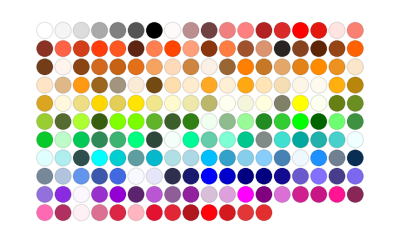

```mathematica
ColorData["Legacy","Image"]
```

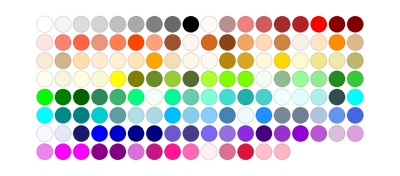

```mathematica
ColorData["HTML","Image"]
```

```mathematica
ColorData["GeologicAges","ColorRules"]
```

{Phanerozoic→RGBColor[0.690196, 0.886275, 0.819608],Cenozoic→RGBColor[1., 1., 0.],Quaternary→RGBColor[1., 1., 0.301961],Holocene→RGBColor[1., 1., 0.701961],Pleistocene→RGBColor[1., 0.921569, 0.384314],Neogene→RGBColor[0.992157, 0.8, 0.541176],Pliocene→RGBColor[0.996078, 0.921569, 0.67451],Miocene→RGBColor[1., 0.870588, 0.],Paleogene→RGBColor[1., 0.701961, 0.],Oligocene→RGBColor[0.917647, 0.776471, 0.447059],Eocene→RGBColor[0.917647, 0.678431, 0.262745],Paleocene→RGBColor[0.921569, 0.576471, 0.00392157],Mesozoic→RGBColor[0.498039, 0.678431, 0.317647],Cretaceous→RGBColor[0.498039, 0.764706, 0.109804],UpperCretaceous→RGBColor[0.870588, 0.945098, 0.592157],LowerCretaceous→RGBColor[0.701961, 0.87451, 0.498039],Jurassic→RGBColor[0.301961, 0.705882, 0.494118],UpperJurassic→RGBColor[0.8, 0.921569, 0.772549],MiddleJurassic→RGBColor[0.498039, 0.792157, 0.576471],LowerJurassic→RGBColor[0.4, 0.752941, 0.572549],Triassic→RGBColor[0.403922, 0.764706, 0.717647],UpperTriassic→RGBColor[0.8, 0.92549, 0.882353],MiddleTriassic→RGBColor[0.6, 0.843137, 0.745098],LowerTriassic→RGBColor[0.403922, 0.701961, 0.623529],Paleozoic→RGBColor[0.501961, 0.709804, 0.835294],Permian→RGBColor[0.403922, 0.776471, 0.866667],Lopingian→RGBColor[0.701961, 0.890196, 0.933333],Guadalupian→RGBColor[0.6, 0.847059, 0.847059],Cisuralian→RGBColor[0.501961, 0.807843, 0.788235],Carboniferous→RGBColor[0.6, 0.741176, 0.854902],Pennsylvanian→RGBColor[0.407843, 0.623529, 0.792157],Mississippian→RGBColor[0.501961, 0.568627, 0.678431],Devonian→RGBColor[0.6, 0.6, 0.788235],UpperDevonian→RGBColor[0.796078, 0.741176, 0.862745],MiddleDevonian→RGBColor[0.6, 0.513725, 0.745098],LowerDevonian→RGBColor[0.501961, 0.490196, 0.729412],Silurian→RGBColor[0.694118, 0.447059, 0.713725],Pridoli→RGBColor[0.913725, 0.780392, 0.886275],Ludlow→RGBColor[0.792157, 0.654902, 0.819608],Wenlock→RGBColor[0.694118, 0.537255, 0.701961],Llandovery→RGBColor[0.596078, 0.345098, 0.658824],Ordovician→RGBColor[0.976471, 0.505882, 0.65098],UpperOrdovician→RGBColor[0.984314, 0.705882, 0.741176],MiddleOrdovician→RGBColor[0.980392, 0.603922, 0.694118],LowerOrdovician→RGBColor[0.901961, 0.490196, 0.643137],Cambrian→RGBColor[0.984314, 0.501961, 0.372549],UpperCambrian→RGBColor[0.992157, 0.803922, 0.721569],MiddleCambrian→RGBColor[0.909804, 0.682353, 0.592157],LowerCambrian→RGBColor[0.905882, 0.486275, 0.447059],Precambrian→RGBColor[0.698039, 0.52549, 0.32549],Proterozoic→RGBColor[0.8, 0.847059, 0.568627],Neoproterozoic→RGBColor[0.792157, 0.647059, 0.584314],Ediacaran→RGBColor[0.917647, 0.847059, 0.737255],Cryogenian→RGBColor[0.862745, 0.670588, 0.666667],Tonian→RGBColor[0.796078, 0.643137, 0.423529],Mesoproterozoic→RGBColor[0.866667, 0.760784, 0.533333],Stenian→RGBColor[0.866667, 0.760784, 0.533333],Ectasian→RGBColor[0.866667, 0.760784, 0.533333],Calymmian→RGBColor[0.866667, 0.760784, 0.533333],Paleoproterozoic→RGBColor[0.701961, 0.698039, 0.368627],Statherian→RGBColor[0.701961, 0.698039, 0.368627],Orosirian→RGBColor[0.701961, 0.698039, 0.368627],Rhyacian→RGBColor[0.701961, 0.698039, 0.368627],Siderian→RGBColor[0.701961, 0.698039, 0.368627],Archean→RGBColor[0.6, 0.678431, 0.67451],Neoarchean→RGBColor[0.796078, 0.803922, 0.784314],Mesoarchean→RGBColor[0.698039, 0.709804, 0.686275],Paleoarchean→RGBColor[0.6, 0.592157, 0.568627],Eoarchean→RGBColor[0.501961, 0.564706, 0.564706],Hadean→RGBColor[0.5, 0.5, 0.56]}

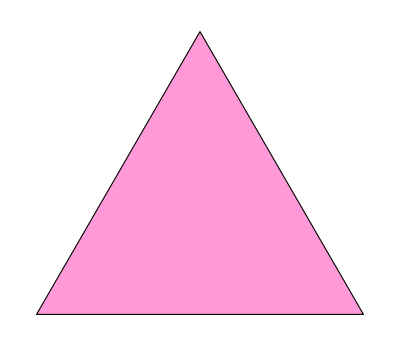
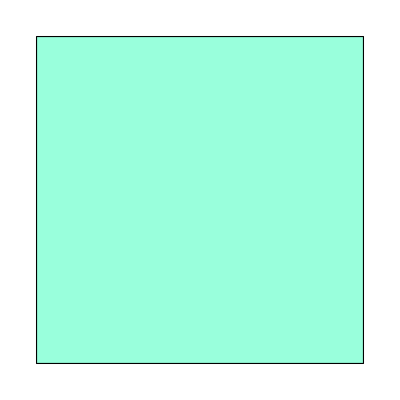
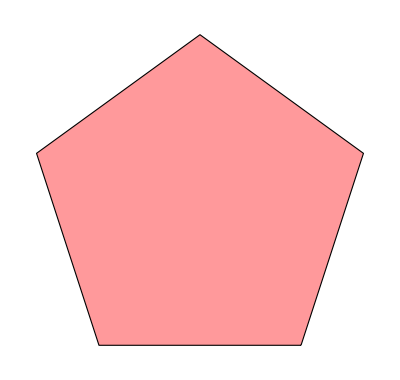
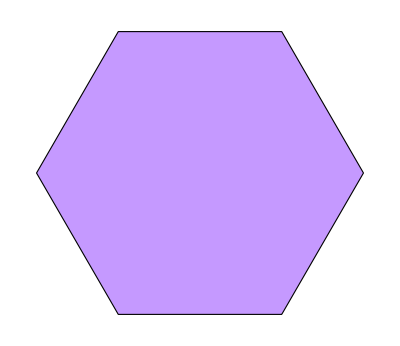
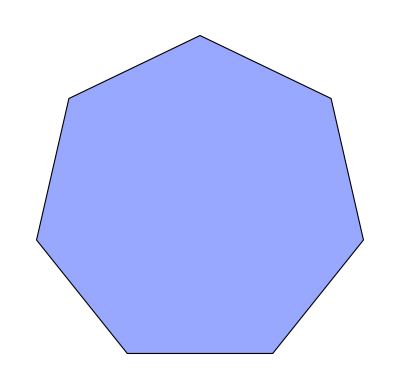
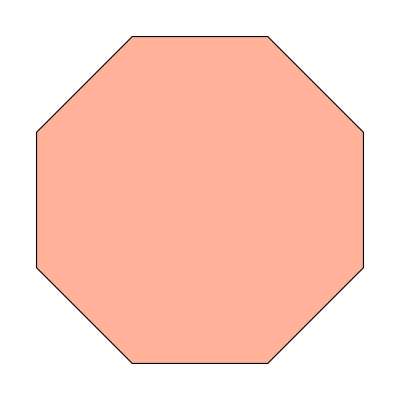
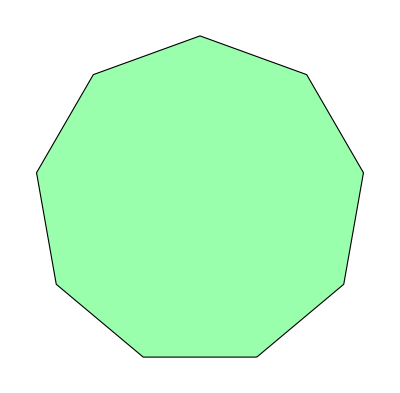
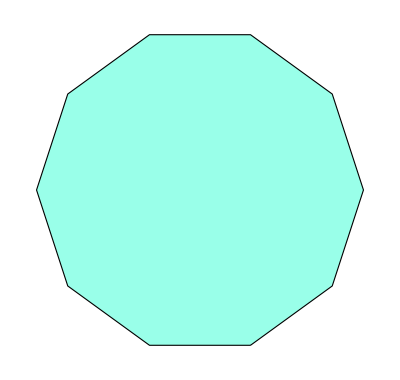

```mathematica
Graphics[{EdgeForm[Black],FaceForm[{Opacity[0.4],Hue[RandomReal[]]}],RegularPolygon[#]}]&/@Range[3,10]
```

## Manipulation

```mathematica
Manipulate[BarChart[RandomInteger[{5,20},a]],{a,5,10,1}]
```

```mathematica
Manipulate[Graphics[Table[{Hue[t/n],Thick, 
   Circle[{Cos[2 Pi t/n], Sin[2 Pi t/n]}, 1]}, {t, n}]],{{n,10},3,30,1}]
```

```mathematica
a=ExampleData[{"TestImage", "Mandrill"}]
```

-Graphics-

```mathematica
Manipulate[Binarize[a,t],{{t,0.5},0,1}]
```

## Strings and Text

```mathematica
Take[WordList[],100]
```

{a,aah,aardvark,aback,abacus,abaft,abalone,abandon,abandoned,abandonment,abase,abasement,abash,abashed,abashment,abate,abatement,abattoir,abbe,abbess,abbey,abbot,abbreviate,abbreviated,abbreviation,abdicate,abdication,abdomen,abdominal,abduct,abducting,abduction,abductor,abeam,abed,aberrant,aberration,abet,abettor,abeyance,abhor,abhorrence,abhorrent,abidance,abide,abiding,ability,abject,abjection,abjectly,abjuration,abjure,ablate,ablated,ablation,ablative,ablaze,able,abloom,ablution,ably,abnegate,abnegation,abnormal,abnormality,abnormally,aboard,abode,abolish,abolition,abolitionism,abolitionist,abominable,abominably,abominate,abomination,aboriginal,aborigine,abort,abortion,abortionist,abortive,abortively,abound,abounding,about,above,aboveboard,abracadabra,abrade,abrasion,abrasive,abrasiveness,abreast,abridge,abridged,abridgment,abroad,abrogate,abrogation}

```mathematica
wordsLengthCounts = Counts[StringLength[WordList[]]]
```

<|1→2,3→596,8→5770,5→3034,6→4622,7→5515,9→5416,11→3124,4→1914,10→4387,12→2094,14→661,16→159,13→1356,15→357,2→63,17→70,20→7,18→19,19→8,21→1,23→1|>

```mathematica
ListPlot[wordsLengthCounts,Filling->0,AxesLabel->{"Word Length","Counts"},Ticks->{Keys[wordsLengthCounts],Automatic}]
```

-Graphics-

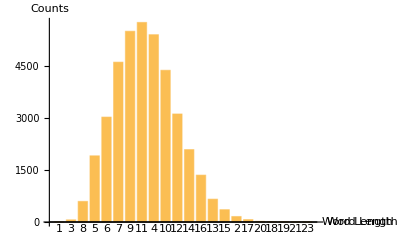

```mathematica
BarChart[KeySort[wordsLengthCounts],AxesLabel->{"Word Length","Counts"},ChartLabels->Keys[wordsLengthCounts]]
```

```mathematica
extrudeText[text_]:=Block[{img,res},
img=Rasterize[Style[text,100]];
res = ImageMesh[img];
RegionProduct[res,Line[{{0.},{10.}}]]
]
```

```mathematica
extrudeText["ABC"]
```

-Graphics3D-

## Arrays, lists of lists

```mathematica
Table[i*j, {i,5},{j,6}] //Grid
```

1 | 2 | 3 | 4 | 5 | 6
2 | 4 | 6 | 8 | 10 | 12
3 | 6 | 9 | 12 | 15 | 18
4 | 8 | 12 | 16 | 20 | 24
5 | 10 | 15 | 20 | 25 | 30

```mathematica
ArrayPlot[Table[i*j,{i,5},{j,6}]]
```

-Graphics-

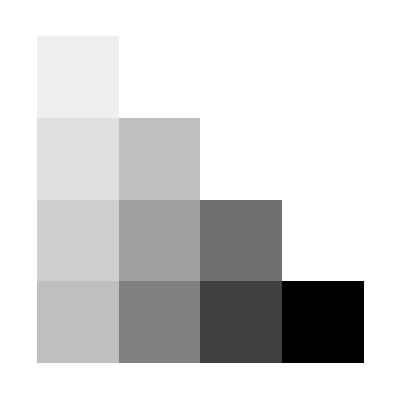

```mathematica
ArrayPlot[Table[i*j,{i,4},{j,i}] ]
```

```mathematica
Graphics[Table[Circle[{0,x},Abs@x],{x,-10,10,0.5}]~Join~Table[Circle[{x,0},Abs@x],{x,-10,10,1}]]
```

-Graphics-

```mathematica
Graphics3D[Table[Sphere[{x,y,z},0.5],{x,10},{y,x},{z,y}],Boxed->False]
```

-Graphics3D-

## Real-World Data

```mathematica
LinguisticAssistant
```

United States

```mathematica
InputForm[LinguisticAssistant]
```

"Entity[\"Country\", \"UnitedStates\"]"

```mathematica
CountryData["UnitedStates"]
```

United States

```mathematica
InputForm[CountryData["UnitedStates"]]
```

"Entity[\"Country\", \"UnitedStates\"]"

```mathematica
LinguisticAssistant
```

```mathematica
InputForm[LinguisticAssistant]
```

"Quantity[2.6, \"Hours\"]"

```mathematica
Quantity[2.6, "Hours"]
```

2.6 h

```mathematica
Quantity[7.5, "Feet"] + Quantity[14, "cm"]
```

242.6 cm

```mathematica
LinguisticAssistant+LinguisticAssistant
```

242.6 cm

```mathematica
N@UnitConvert[Quantity[100,"lb"],"kg"]
```

45.3592 kg

```mathematica
EarthquakeData[Entity["Earthquake","nc73666231"]]
```

Missing[NotAvailable]

{"type":"Feature","properties":{"mag":6.2,"place":"38km W of Petrolia, CA","time":1640031019100,"updated":1640430417695,"tz":null,"url":"https://earthquake.usgs.gov/earthquakes/eventpage/nc73666231","detail":"https://earthquake.usgs.gov/earthquakes/feed/v1.0/detail/nc73666231.geojson","felt":4372,"cdi":7,"mmi":6.936,"alert":"yellow","status":"reviewed","tsunami":1,"sig":1350,"net":"nc","code":"73666231","ids":",ew1640031020,nc73666231,at00r4fk16,us6000gdxq,","sources":",ew,nc,at,us,","types":",dyfi,focal-mechanism,general-text,ground-failure,impact-link,losspager,moment-tensor,nearby-cities,oaf,origin,phase-data,scitech-link,shake-alert,shakemap,","nst":118,"dmin":0.2951,"rms":0.22,"gap":224,"magType":"mw","type":"earthquake","title":"M 6.2 - 38km W of Petrolia, CA"},"geometry":{"type":"Point","coordinates":[-124.727,40.314,14.85]},"id":"nc73666231"}

```mathematica
data = EarthquakeData[GeoPosition[{40.31,-124.7 }],6]
```

<|centennial625301→<|Period→July 26, 1890 3:40 amGMT-6,AzimuthalGap→Missing[NotAvailable],Depth→Missing[NotAvailable],5,Position→GeoPosition[{40.5,-124.2}],PositionMethod→Missing[NotAvailable]|>,23,ncnc73666231→<|Period→1,8,1|>|>
 |  |  |  |

```mathematica
EarthquakeData[Entity["Earthquake","ncnc73666231"]]
```

<|Period→December 20, 2021 2:10 pmGMT-6,Magnitude→6.2,Position→GeoPosition[{40.314,-124.727}]|>

```mathematica
mintemp=(Normal@WeatherData["KBMG","MinTemperature",{{#,12,25},{#,12,25},"Day"}])&/@Range[1991,2021,1];
```

```mathematica
maxtemp=(Normal@WeatherData["KBMG","MaxTemperature",{{#,12,25},{#,12,25},"Day"}])&/@Range[1991,2021,1];
```

```mathematica
mintemp = DeleteMissing[Flatten[mintemp,1]]
```

{{December 25, 1991 12:00 amGMT-6,-6 °C},{December 25, 1992 12:00 amGMT-6,-7.28 °C},{December 25, 1993 12:00 amGMT-6,-10 °C},{December 25, 1994 12:00 amGMT-6,-1.72 °C},{December 25, 1995 12:00 amGMT-6,-5 °C},{December 25, 1996 12:00 amGMT-6,-11 °C},{December 25, 1998 12:00 amGMT-6,-12.78 °C},{December 25, 1999 12:00 amGMT-6,-16 °C},{December 25, 2000 12:00 amGMT-6,-23 °C},{December 25, 2001 12:00 amGMT-6,-9.39 °C},{December 25, 2002 12:00 amGMT-6,-4 °C},{December 25, 2003 12:00 amGMT-6,-6 °C},{December 25, 2004 12:00 amGMT-6,-28.28 °C},{December 25, 2005 12:00 amGMT-6,1 °C},{December 25, 2006 12:00 amGMT-6,1.72 °C},{December 25, 2007 12:00 amGMT-6,-6.72 °C},{December 25, 2008 12:00 amGMT-6,-9.39 °C},{December 25, 2009 12:00 amGMT-6,-1.11 °C},{December 25, 2011 12:00 amGMT-6,0.61 °C},{December 25, 2012 12:00 amGMT-6,-1.11 °C},{December 25, 2013 12:00 amGMT-6,-8.28 °C},{December 25, 2014 12:00 amGMT-6,2.22 °C},{December 25, 2015 12:00 amGMT-6,10 °C},{December 25, 2016 12:00 amGMT-6,2.22 °C},{December 25, 2017 12:00 amGMT-6,-7 °C},{December 25, 2018 12:00 amGMT-6,0 °C},{December 25, 2019 12:00 amGMT-6,-1.11 °C},{December 25, 2020 12:00 amGMT-6,-12.22 °C},{December 25, 2021 12:00 amGMT-6,16.72 °C}}

```mathematica
maxtemp = DeleteMissing[Flatten[maxtemp,1]]
```

{{December 25, 1991 12:00 amGMT-6,10 °C},{December 25, 1992 12:00 amGMT-6,1.61 °C},{December 25, 1993 12:00 amGMT-6,-2.78 °C},{December 25, 1994 12:00 amGMT-6,8.78 °C},{December 25, 1995 12:00 amGMT-6,-4.5 °C},{December 25, 1996 12:00 amGMT-6,-3 °C},{December 25, 1998 12:00 amGMT-6,-0.61 °C},{December 25, 1999 12:00 amGMT-6,-3 °C},{December 25, 2000 12:00 amGMT-6,-7 °C},{December 25, 2001 12:00 amGMT-6,-1.72 °C},{December 25, 2002 12:00 amGMT-6,-2 °C},{December 25, 2003 12:00 amGMT-6,2 °C},{December 25, 2004 12:00 amGMT-6,-5.61 °C},{December 25, 2005 12:00 amGMT-6,7 °C},{December 25, 2006 12:00 amGMT-6,5 °C},{December 25, 2007 12:00 amGMT-6,8.89 °C},{December 25, 2008 12:00 amGMT-6,1.11 °C},{December 25, 2009 12:00 amGMT-6,9.39 °C},{December 25, 2011 12:00 amGMT-6,1.72 °C},{December 25, 2012 12:00 amGMT-6,1.11 °C},{December 25, 2013 12:00 amGMT-6,-6.72 °C},{December 25, 2014 12:00 amGMT-6,3.28 °C},{December 25, 2015 12:00 amGMT-6,12.22 °C},{December 25, 2016 12:00 amGMT-6,5.61 °C},{December 25, 2017 12:00 amGMT-6,-5.61 °C},{December 25, 2018 12:00 amGMT-6,8.28 °C},{December 25, 2019 12:00 amGMT-6,18.89 °C},{December 25, 2020 12:00 amGMT-6,-7.22 °C},{December 25, 2021 12:00 amGMT-6,17.78 °C}}

```mathematica
DateListPlot[{maxtemp,mintemp},PlotTheme->"Scientific",Filling->{1 -> {2}},PlotLabel->"Min/Max Temperature on Christmas Day 1991-2021",Mesh->Full,PlotMarkers->Automatic,PlotLegends->{"Max","Min"},FrameLabel->{"Year","Temperature°"},LabelStyle->{Bold,FontSize->12},ImageSize->800,PerformanceGoal->"Quality"]
```

-Graphics-

```mathematica
Normal[a]
```

{{December 25, 2021 12:00 amGMT-6,17.22 °C}}